```mathematica
c19 = {46722,34638,62084,132930,207088,273201,317067,334073,339091,336055,324535,302135,279431,256731,233107,210700,190089,169635,150732,133141,117116,101956,88686,76681,65325,54863,45830,37354,29997,23823,18384,14758,12078,9970,8435,6981,5927,5125,4507,4049,3508,3134,2782,2496,2269,2045};
c20 = {23674,17589,29465,61370,99009,131994,152524,161997,165797,164198,159452,151221,140831,131117,118890,107848,98412,88335,79673,71530,62856,55356,48373,40664,35245,29511,24043,19668,15922,12496,9430,7515,6081,4971,4279,3476,2930,2544,2166,1965,1747,1481,1312,1115,1024,951};
```

```mathematica
tiempos = Subdivide[Length[c19]];
```

```mathematica
puntos19 = Table[{i,c19[[i]]},{i,Length[c19]}];
puntos20 = Table[{i,c20[[i]]},{i,Length[c19]}];
```

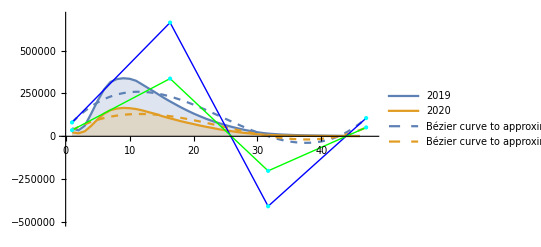

```mathematica
n=3;
puntosControl19=N[approx[puntos19,tiempos,n]]; (*Puntos de control*)
puntosControl19Dibujo=Table[{PointSize->Large,Cyan,Point[puntosControl19[[i]]]},{i,Length[puntosControl19]}]; 
bezier19[t_]:=CurvaBezier[puntosControl19][t]

puntosControl20=N[approx[puntos20,tiempos,n]]; (*Puntos de control*)
puntosControl20Dibujo=Table[{PointSize->Large,Cyan,Point[puntosControl20[[i]]]},{i,Length[puntosControl20]}]; 
bezier20[t_]:=CurvaBezier[puntosControl20][t] 
Show[
ListPlot[{c19,c20},Filling->Axis,Joined->True,PlotRange->{{0,48},{-500000.3779058023,700000.9485048489}},PlotLegends->{"2019","2020"}],
ParametricPlot[{bezier19[t],bezier20[t]},{t,0,1},PlotStyle->Dashed,PlotLegends->{"Bézier curve to approximate 2019","Bézier curve to approximate 2020"}],
Graphics[{Blue,Line[puntosControl19],PointSize[Medium],puntosControl19Dibujo,Green,Line[puntosControl20],PointSize[Medium],puntosControl20Dibujo}]

]
```

```mathematica
puntosControl19
```

{{1.,80905.},{16.3333,664433.},{31.6667,-408684.},{47.,106333.}}

```mathematica
p1 = Show[
ListPlot[{c19,c20},Filling->Axis,Joined->True,PlotRange->{{0,48},{-500000.3779058023,700000.9485048489}},PlotLegends->{"2019","2020"}],
ParametricPlot[{bezier19[t],bezier20[t]},{t,0,1},PlotStyle->Dashed,PlotLegends->{"Bézier curve to approximate 2019","Bézier curve to approximate 2020"}],
Graphics[{Blue,Line[puntosControl19],PointSize[Medium],puntosControl19Dibujo,Green,Line[puntosControl20],PointSize[Medium],puntosControl20Dibujo}]

]
```

```mathematica
SetDirectory["D:\\Desktop\\Estudios\\UNIVERSIDAD\\Investmat\\TFM\\codigos_final_2\\graphics_new"]
```

D:\Desktop\Estudios\UNIVERSIDAD\Investmat\TFM\codigos_final_2\graphics_new

```mathematica
Export["bezier_curvas_tiempos_ejemplo.png",p1]
```

bezier_curvas_tiempos_ejemplo.png